## Simple test

```mathematica
xdata[x0_,dev_,n_]:=Table[x0+RandomChoice[{-1,1}]*dev,{i,1,n,1}];
plotdata[data_]:=ListPlot[data,Joined->True,Frame->True,Axes->False,PlotMarkers->{Automatic, Medium}];
```

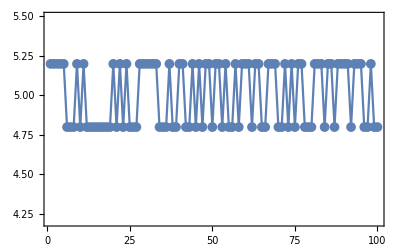

```mathematica
w=xdata[5,0.2,100];
Show[plotdata[w],PlotRange->{4.2,5.5}]
```